### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

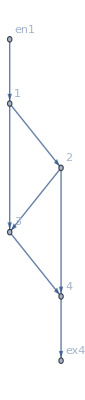

```mathematica
d2e["FG"]
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->40,U1->0, S1->1,S2->1,S3->1,S4->1,S5->1,S6->1, S7->1,S8->1,S9->1,S10->0,S11->0,S12->0,S13->1,S14->1,S15->0,S16->0}]])//AbsoluteTiming
```

D2E: Variables are all set

Second check:

DataToEquations: Triangle inequalities for switching costs: <|{2,1,3,1}→False,{3,1,2,1}→False|>

DataToEquations: The switching costs are incompatible. 
Stopping!

{0.045905,CriticalCongestionSolver2[Null]}

```mathematica
Select[<|{1,2,4,1}->True,{1,2,3,1}->True,{3,2,1,1}->True,{3,2,4,1}->True,{4,2,1,1}->True,{4,2,3,1}->True,{1,3,4,1}->False,{4,3,1,0}->True,{1,3,2,0}->True,{2,3,1,0}->True,{3,4,2,0}->True,{2,4,3,0}->True,{2,3,4,0}->True,{4,3,2,0}->True,{3,1,2,0}->True,{2,1,3,0}->True|>, Function[exp,!TrueQ[exp]]]
```

<|{1,3,4,1}→False|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->800,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}]])//AbsoluteTiming
```

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CCS2: EliminateVarsSimplify for the us

$Aborted

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->800,U1->15, S1->1,S2->1,S3->1,S4->1,S5->1,S6->1, S7->1,S8->1,S9->1,S10->1,S11->1,S12->1,S13->1,S14->1,S15->1,S16->1}]])//AbsoluteTiming
```

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CCS2: EliminateVarsSimplify for the us

$Aborted

$Aborted

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->40,U1->0, S1->0,S2->0,S3->0,S4->0,S5->0,S6->0, S7->100,S8->100,S9->100,S10->100,S11->100,S12->0,S13->0,S14->0,S15->0,S16->0}]])//AbsoluteTiming
```

D2E: Variables are all set

D2E: CleanEqualities for the values at the auxiliary edges

D2E: Assembled most elements of the system

D2E: CleanEqualities for the switching conditions on each vertex

D2E: CleanEqualities for the complementary conditions (given the rules)

D2E: CleanEqualities for the balance conditions in terms of (mostly) transition currents

D2E: CleanEqualities for the (non) critical case equations

D2E: D2E is finished!

CCS2: EliminateVarsSimplify for the us

CCS2: Not finished with the us!

CCS2: Reducing further (NewReduce)...

CCS2: Simplifying...

CCS2: Finished with the us!

CCS2: Finished with the js!

{9.62355,<|u1→200/3,u2→80/3,u3→200/3,u4→200/3,u5→80/3,u6→40/3,u7→80/3,u8→0,u9→40/3,u10→0,u11→0,u12→0,u13→200/3,u14→200/3,j1→0,j2→40,j3→0,j4→0,j5→0,j6→40/3,j7→0,j8→80/3,j9→0,j10→40/3,j11→0,j12→40,j13→0,j14→40|>}

```mathematica
d2e["jvars"]
```

<|{1,1->2}→j1,{2,1->2}→j2,{1,1->3}→j3,{3,1->3}→j4,{2,2->3}→j5,{3,2->3}→j6,{2,2->4}→j7,{4,2->4}→j8,{3,3->4}→j9,{4,3->4}→j10,{4,4->ex4}→j11,{ex4,4->ex4}→j12,{en1,en1->1}→j13,{1,en1->1}→j14|>

```mathematica
d2e["FG"]
```

-Graphics-

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 9.45231 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j418==40&&j419==40&&j420==0&&j421==40&&j422==40&&j425==0&&j427==0&&jt438==0&&jt444==0&&u456==96&&u457==96&&55≤u458≤56&&u459==55&&u460==55&&u462==96
and the rules are:
<|j424→80,u468→15,j423→80,j426→-80+j418+j419-j425,j428→-j418+j420+j421+j425-j427,j429→-80+j418-j420+j422-j425+j427,j430→0,j431→0,jt432→j425,jt433→0,jt434→-80+j418+j419-j425,jt435→0,jt436→80-j419+j425,jt437→j419-j425,jt439→j418-jt438,jt440→j418-j421+j427-jt438,jt441→-j418+j421+jt438,jt442→-j418+j421+j425-j427+jt438,jt443→j420-jt438,jt445→j419-jt444,jt446→j419+j420-j422-jt444,jt447→-j419+j422+jt444,jt448→-80+j418-j420+j422-j425+jt444,jt449→j427-jt444,jt450→-80+j418-j420+j422-j425+j427,jt451→80-j418+j420+j421-j422+j425-j427,jt452→-j418+j420+j421+j425-j427,jt453→j418-j420-j421+j422-j425+j427,jt454→0,jt455→0,u461→15,u463→-j418+j425+u456,u464→-80+j418-j425+u457,u465→-j420+j427+u458,u466→-j418+j420+j425-j427+u459,u467→-80+j418-j420-j425+j427+u460,u469→u462|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{55≤u458≤56,<|j424→80,u468→15,j423→80,j426→-80+40+40-0,j428→-40+0+40+0-0,j429→-80+40-0+40-0+0,j430→0,j431→0,jt432→0,jt433→0,jt434→-80+40+40-0,jt435→0,jt436→80-40+0,jt437→40-0,jt439→40-0,jt440→40-40+0-0,jt441→-40+40+0,jt442→-40+40+0-0+0,jt443→0-0,jt445→40-0,jt446→40+0-40-0,jt447→-40+40+0,jt448→-80+40-0+40-0+0,jt449→0-0,jt450→-80+40-0+40-0+0,jt451→80-40+0+40-40+0-0,jt452→-40+0+40+0-0,jt453→40-0-40+40-0+0,jt454→0,jt455→0,u461→15,u463→-40+0+96,u464→-80+40-0+96,u465→-0+0+u458,u466→-40+0+0-0+55,u467→-80+40-0-0+0+55,u469→96,j418→40,j419→40,j420→0,j421→40,j422→40,j425→0,j427→0,jt438→0,jt444→0,u456→96,u457→96,u459→55,u460→55,u462→96|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{11.0062,Null}

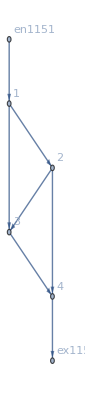

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j418→40,j419→40,j420→0,j421→40,j422→40,j423→80,j424→80,j425→0,j426→0,j427→0,j428→0,j429→0,j430→0,j431→0,jt432→0,jt433→0,jt434→0,jt435→0,jt436→40,jt437→40,jt438→0,jt439→40,jt440→0,jt441→0,jt442→0,jt443→0,jt444→0,jt445→40,jt446→0,jt447→0,jt448→0,jt449→0,jt450→0,jt451→40,jt452→0,jt453→40,jt454→0,jt455→0,u456→96,u457→96,u459→55,u460→55,u461→15,u462→96,u463→56,u464→56,u465→u458,u466→15,u467→15,u468→15,u469→96|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```